# 连续线绘图

用连续线绘图表示列奥纳多·达·芬奇的蒙娜·丽莎 .

```mathematica
monalisa=Entity["Artwork","MonaLisa::LeonardoDaVinci"][EntityProperty["Artwork","Image"]]
```

-Graphics-

```mathematica
monalisa = -Graphics-;
```

将图像转换成点 .

```mathematica
monalisa=ColorQuantize[ColorConvert[monalisa,"Grayscale"],2];
```

```mathematica
pos=PixelValuePositions[ImageAdjust[monalisa],0];
```

绘制蒙娜·丽莎 .

```mathematica
res=FindShortestTour[pos];
```

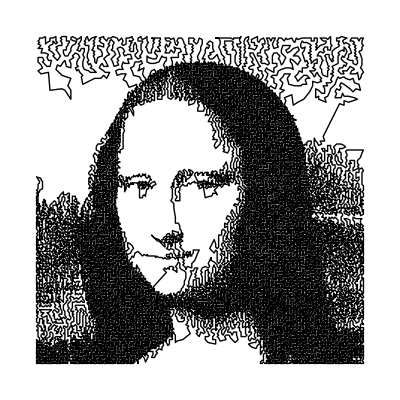

```mathematica
Graphics[Line[pos[[res[[2]]]]]]
```

```mathematica
a=Audio["E:\\KuGou\\kanon - 雪之少女.mp3"]
```

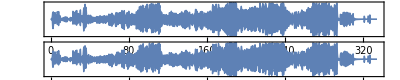

```mathematica
AudioPlot[a]
```

```mathematica
AudioData[a]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,14754742,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},1}
 |  |  |  |

```mathematica
hfc=Rescale@AudioLocalMeasurements[a,"HighFrequencyContent"];
```

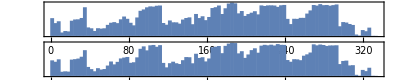

```mathematica
Quiet@AudioPlot[a,PlotRange->{All,All},Appearance->"DiscreteAbs",ColorFunction->Function[{x,y},ColorData["SunsetColors"]@hfc[x]]]
```